## Newton — Problem Set 4 — Solution

### 1. A Very Strange Central Force Law

### 2. Radii of Curvature — Newton’s Construction Involving Chords

(a) Below is a table showing the x-value, the slope of the chord leading to that x-value, and the place on the y-axis where the perpendicular to the chord intersects it.

```mathematica
twoAPerpendicular[x_]:=-x/(-Sqrt[1-x^2]+1)
```

```mathematica
MatrixForm[Table[{x,twoAPerpendicular[x], -x twoAPerpendicular[x]+(-Sqrt[1-x^2]+1)}, {x,DeleteCases[Range[-0.5, 0.5, 0.1],0.0]}]]
```

(-0.5 | 3.73205 | 2.
-0.4 | 4.79129 | 2.
-0.3 | 6.51313 | 2.
-0.2 | 9.89898 | 2.
-0.1 | 19.9499 | 2.
0.1 | -19.9499 | 2.
0.2 | -9.89898 | 2.
0.3 | -6.51313 | 2.
0.4 | -4.79129 | 2.
0.5 | -3.73205 | 2.)

On the next page, I have plotted these results. Notice that for the circle, all the points go to exactly the same place. This is a property of the circle, not of other curves that are close to circular.

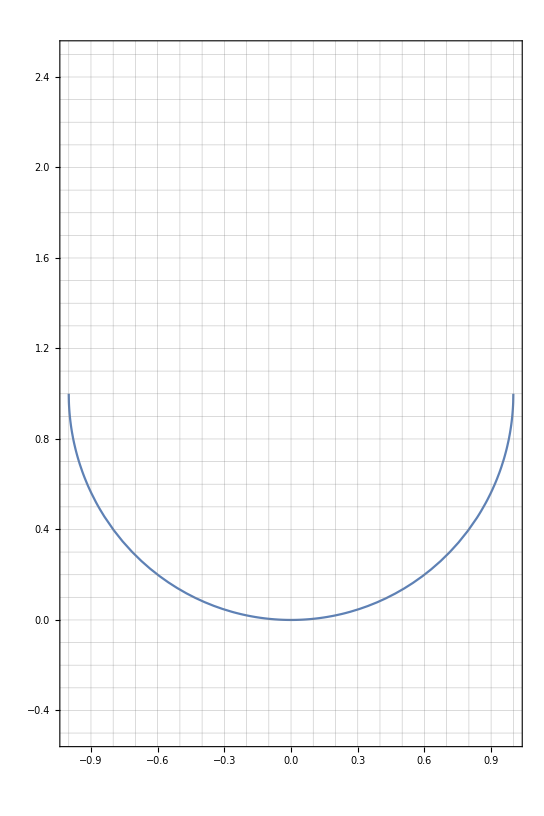

```mathematica
Plot[-Sqrt[1-x^2]+1, {x, -1, 1}, PlotRange->{{-1, 1}, {-0.5, 2.5}}, AspectRatio->3/2, GridLines->{Range[-1, 1, 0.1], Range[-0.5, 2.5, 0.1]}, Frame->True]
```

(b) Below is a table showing the x-value, the slope of the chord leading to that x-value, and the place on the y-axis where the perpendicular to the chord intersects it.

```mathematica
twoBPerpendicular[x_]:=-x/(5 x^4)
```

```mathematica
MatrixForm[Table[{x,twoBPerpendicular[x], -x twoBPerpendicular[x]+(5 x^4)}, {x,DeleteCases[Range[-1, 1, 0.1],0.0]}]]
```

(-1. | 0.2 | 5.2
-0.9 | 0.274348 | 3.52741
-0.8 | 0.390625 | 2.3605
-0.7 | 0.58309 | 1.60866
-0.6 | 0.925926 | 1.20356
-0.5 | 1.6 | 1.1125
-0.4 | 3.125 | 1.378
-0.3 | 7.40741 | 2.26272
-0.2 | 25. | 5.008
-0.1 | 200. | 20.0005
0.1 | -200. | 20.0005
0.2 | -25. | 5.008
0.3 | -7.40741 | 2.26272
0.4 | -3.125 | 1.378
0.5 | -1.6 | 1.1125
0.6 | -0.925926 | 1.20356
0.7 | -0.58309 | 1.60866
0.8 | -0.390625 | 2.3605
0.9 | -0.274348 | 3.52741
1. | -0.2 | 5.2)

On the next page, I have plotted these results. Notice that for the quartic, there isn’t convergence! The origin is a point on this curve with zero curvature.

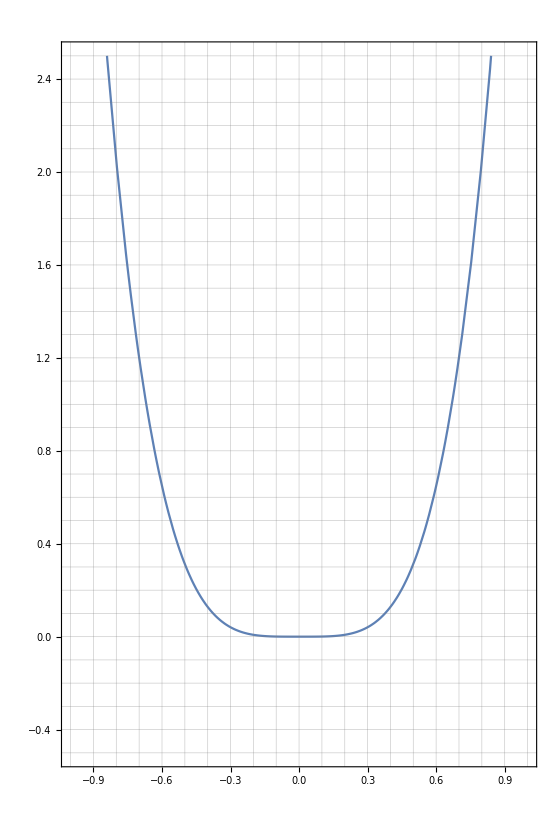

```mathematica
Plot[5 x^4, {x, -1, 1}, PlotRange->{{-1, 1}, {-0.5, 2.5}}, AspectRatio->3/2, GridLines->{Range[-1, 1, 0.1], Range[-0.5, 2.5, 0.1]}, Frame->True]
```

(c) Below is a table showing the x-value, the slope of the chord leading to that x-value, and the place on the y-axis where the perpendicular to the chord intersects it.

```mathematica
twoCPerpendicular[x_]:=-x/(x^3+x^2)
```

```mathematica
MatrixForm[Table[{x,twoCPerpendicular[x], -x twoCPerpendicular[x]+(x^3+x^2)}, {x,DeleteCases[Range[-0.5, 1.0, 0.1],0.0]}]]
```

(-0.5 | 4. | 2.125
-0.4 | 4.16667 | 1.76267
-0.3 | 4.7619 | 1.49157
-0.2 | 6.25 | 1.282
-0.1 | 11.1111 | 1.12011
0.1 | -9.09091 | 0.920091
0.2 | -4.16667 | 0.881333
0.3 | -2.5641 | 0.886231
0.4 | -1.78571 | 0.938286
0.5 | -1.33333 | 1.04167
0.6 | -1.04167 | 1.201
0.7 | -0.840336 | 1.42124
0.8 | -0.694444 | 1.70756
0.9 | -0.584795 | 2.06532
1. | -0.5 | 2.5)

On the next page, I have plotted these results. This is the more typical case that Newton is expecting. Unlike for the circle they don’t converge identically. Unlike the quartic at x=0 though, they do converge.

Although I haven’t plotted the additional ten points below on the next page, they help see numerically that they are converging to 1.0.

```mathematica
MatrixForm[Table[{x,twoCPerpendicular[x], -x twoCPerpendicular[x]+(x^3+x^2)}, {x,Range[-0.09, 0.09, 0.02]}]]
```

(-0.09 | 12.21 | 1.10627
-0.07 | 15.361 | 1.07983
-0.05 | 21.0526 | 1.05501
-0.03 | 34.3643 | 1.0318
-0.01 | 101.01 | 1.0102
0.01 | -99.0099 | 0.9902
0.03 | -32.3625 | 0.971801
0.05 | -19.0476 | 0.955006
0.07 | -13.3511 | 0.939822
0.09 | -10.1937 | 0.92626)

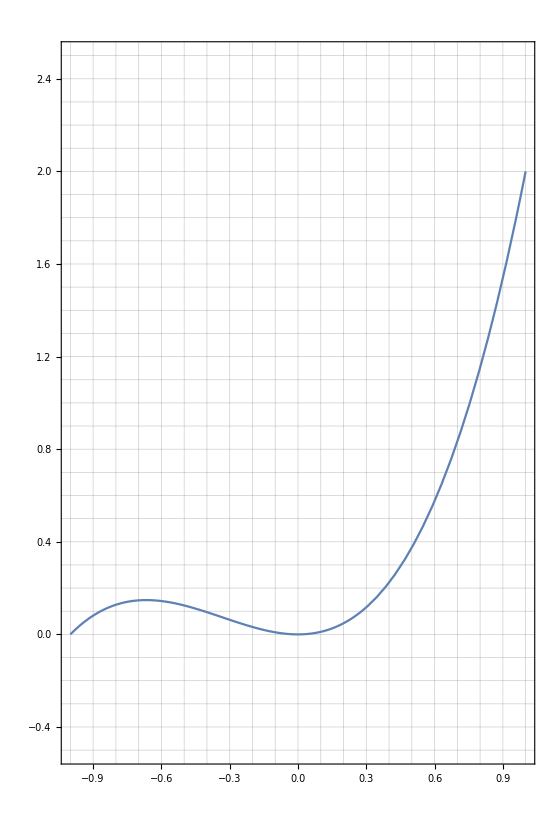

```mathematica
Plot[x^3+x^2, {x, -1, 1}, PlotRange->{{-1, 1}, {-0.5, 2.5}}, AspectRatio->3/2, GridLines->{Range[-1, 1, 0.1], Range[-0.5, 2.5, 0.1]}, Frame->True]
```

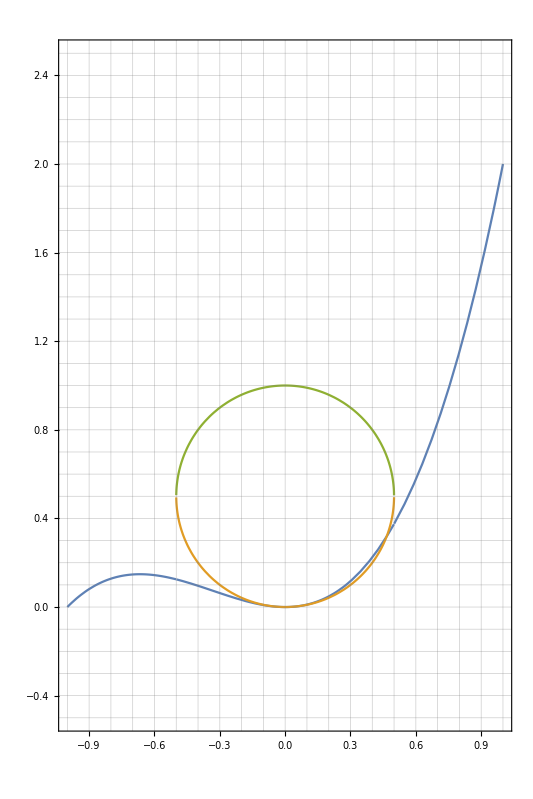

```mathematica
Plot[{x^3+x^2, -Sqrt[0.25-x^2]+0.5, Sqrt[0.25-x^2]+0.5}, {x, -1, 1}, PlotRange->{{-1, 1}, {-0.5, 2.5}}, AspectRatio->3/2, GridLines->{Range[-1, 1, 0.1], Range[-0.5, 2.5, 0.1]}, Frame->True]
```

### 3. Period Associated with the Van Der Waals Force